# Compute the expectation value

Calculate the expectation value of an operator, given a quantum state

## Example Content

The expectation value of an operator with respect to a quantum state can be computed in different ways.

Install and load the QuantumFramework paclet:

```mathematica
PacletInstall["Wolfram/QuantumFramework"]
Needs["Wolfram`QuantumFramework`"]
```

Create a many-body random mixed state:

```mathematica
qs=QuantumState["RandomMixed"[3],"Label"->"ρ"]
```

QuantumState[…]

Create a random many-body Hermitian operator:

```mathematica
op=QuantumOperator["RandomHermitian",Range[3],"Label"->"Random Hermitian"]
```

QuantumOperator[…]

Calculate ⟨A⟩=Tr[A.ρ], which is the expectation value of the operator A, given the density matrix ρ:

```mathematica
Tr[op["Matrix"].qs["DensityMatrix"]]//Chop
```

0.106417

One can feed the density matrix into  a circuit, to find the expectation value:

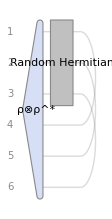

```mathematica
qc=QuantumCircuitOperator[{qs["Bend"],op,Sequence@@Table["Cap"->{i,i+3},{i,3}]}];
qc["Diagram"]
```

Evaluate the circuit and get the scalar result:

```mathematica
qc[]["Scalar"]//Chop
```

0.106417

Transform the density matrix into an operator, then do partial tracing:

```mathematica
QuantumPartialTrace[op[qs["Operator"]]]["Scalar"]//Chop
```

0.106417

Measure the operator, given the state, and find the mean value:

```mathematica
QuantumMeasurementOperator[op][qs]["Mean"]//Chop
```

0.106417

## Supporting Data and Definitions

(Your data can be Dataset[…], EntityStore[…], Image[…], Audio[…] or any other expression)

```mathematica
ResourceData[{{}},"NameOfContent"]=xxxx
```

(xxxx can be your data, or File[…], CloudObject[…] or LocalObject[…] that contains it.)

## Thumbnail Image

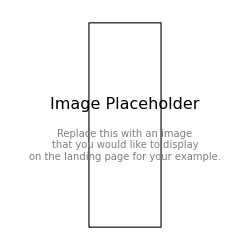

## Source & Additional Information

### Contributed By

Wolfram Research, Quantum Computation Framework Team

### Keywords

Quantum expectation value

Quantum measurement

Quantum mean value

### Categories

Algebra
 Calculus
 Complex Systems
 Control Systems
 Engineering
 Food & Nutrition
 Graphs & Networks
 Machine Learning
 Optimization
 Puzzles and Recreation
 System Modeling
 Video Processing
  |  Astronomy
 Cellular Automata
 Computer Science
 Creative Arts
 Finance & Economics
 Geography
 Image Processing
 Mathematics
 Physics
 Signal Processing
 Text & Language Processing
 Visualization & Graphics
 |  Audio Processing
 Chemistry
 Computer Vision
 Data Science
 Finite Element Method
 Geometry
 Life Sciences
 Notebooks & User Interfaces
 Presentation & Publication
 Social Sciences
 Time-Related Computation
 Quantum Computation

### Related Documentation Pages

Symbol name or documentation URI

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Original Source References and Attributions

Source, reference or citation

### Links

https://resources.wolframcloud.com/PacletRepository/resources/Wolfram/QuantumFramework/

### Compatibility

#### Wolfram Language Version

13.2+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

## Author Notes

Additional information about limitations, issues, etc.